10.

0.00537109

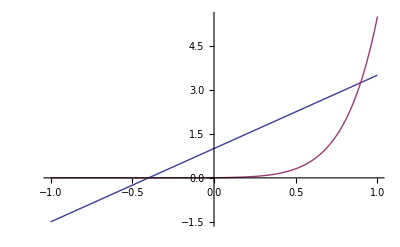

```mathematica
d=2.5;
c=2d/(3-d)
b=(1+c)/2^(1+c)
R1[x_]:=1+d x
R5[x_]:=b(x+1)^c
Plot[{R1[x],R5[x]},{x,-1,1}]
```

```mathematica
Clear[d,a,b]
(*R[x_]:=a(x+1)^1+b(x+1)^10*)
R[x_]:=a (x+1)^b
expr0=Integrate[R[x],{x,-1,1},Assumptions->b>1]
expr1=Integrate[x*R[x],{x,-1,1},Assumptions->b>1]
Solve[{expr0==1,expr1==d/3},{a,b}]
```

(2^(1+b) a)/(1+b)

(2^(1+b) a b)/(2+3 b+b^2)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{a→2^(-1+(2 d)/(-3+d)) (1-(2 d)/(-3+d)),b→-(2 d)/(-3+d)}}

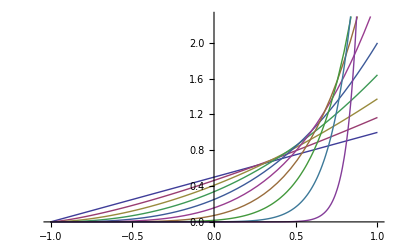

```mathematica
R[x_,d_]:=2^(-1+(2 d)/(-3+d)) (1-(2 d)/(-3+d))(x+1)^(-(2 d)/(-3+d))
Plot[{R[x,1],R[x,1.2],R[x,1.4],R[x,1.6],R[x,1.8],R[x,2],R[x,2.2],R[x,2.4],R[x,2.6],R[x,2.8]},{x,-1,1}]
```

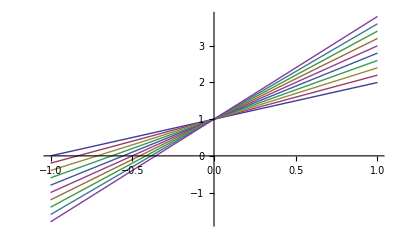

```mathematica
R[x_,d_]:=(1+d x)
Plot[{R[x,1],R[x,1.2],R[x,1.4],R[x,1.6],R[x,1.8],R[x,2],R[x,2.2],R[x,2.4],R[x,2.6],R[x,2.8]},{x,-1,1}]
```